### Технические вещи

```mathematica
Needs["NDSolve`FEM`"]
$HistoryLength=0;
Mon [prog_]:=
Monitor[
Timing[
ReleaseHold[prog];
][[1]],
{
step," / ",tmax," ",
ProgressIndicator[step,{0,tmax}]
}//Row
];
```

## Условия

### Условия:

```mathematica
xmin:=-1
xmax:=5
(*Ω=ImplicitRegion[True,({{x, xmin, xmax}}) ];param=Sequence[x];i=IdentityMatrix[1];*)
Ω:=Rectangle[{xmin,xmin},{xmax,xmax}];X=Sequence[x,y];i=IdentityMatrix[2];

tmax:=10
γ:=4
{{{dnm, dmp, dpn}}}:={{{0.2, 0.01, 0.01}}};
```

```mathematica
rate:={V->γ If[2<x<3 && 2<y<3 &&m[t,X]≥0.0001,ifa,0]};
```

```mathematica
(*bcs := {
  NeumannValue[0, x == xmin || x == xmax],
  NeumannValue[0, x == xmin || x == xmax]
  }*)
bcs := {
    NeumannValue[0, x == xmin || x == xmax || y == xmin || y == xmax],
    NeumannValue[0, x == xmin ||  x == xmax ||  y == xmin || y == xmax]
    }
(*bcs := {
  NeumannValue[0, x == xmin || x == xmax],
  NeumannValue[0, x == xmin || x == xmax]
  }*)
```

### Уравнения

```mathematica
eq:=Inactivate[
{
D[n[t,X], {t}]+jN{X},
D[p[t,X], {t}]+jP{X}-V
},
Div|D|Grad];
```

```mathematica
ics:={
{n[0,X],p[0,X]}=={0.1,0.001}
};
```

```mathematica
flux:=Inactivate[
{
jN->-(m[t,X] dNM).n[t,X]{X}-(p[t,X] dPN).n[t,X]{X}+(n[t,X] dNM).m[t,X]{X}+(n[t,X] dPN).p[t,X]{X},
jP->-(m[t,X] dMP).p[t,X]{X}-(n[t,X] dPN).p[t,X]{X}+(p[t,X] dMP).m[t,X]{X}+(p[t,X] dPN).n[t,X]{X}
},
Div|D|Grad];
{dNM,dMP,dPN}={i*dnm,i*dmp,i*dpn};
```

```mathematica
rep:={
ifa->0.7 m[t,X](-Log[m[t,X]/(1-n[t,X])])^((γ-1.)/γ),
m[t,X]->1-n[t,X]-p[t,X]
};
```

```mathematica
solve := NDSolve[
{pde == bcs, ics}, 
{n, p}, {t, 0., tmax}, {X} ∈ Ω, 
EvaluationMonitor :> Sow[step = t], 
Method -> {
"PDEDiscretization" -> 
{"MethodOfLines", 
"SpatialDiscretization" -> 
{"FiniteElement", 
"MeshOptions" -> {"MaxCellMeasure" -> 0.01, "MeshOrder" -> 2}, 
"IntegrationOrder" -> 3}
}}]
```

### Check

```mathematica
solveCheck:=NDSolve`ProcessEquations[
solPDE,
{n,p},
{t,0.,tmax},
{x,xmin,xmax}(*,
Method->{
"PDEDiscretization"->{
"MethodOfLines",
"SpatialDiscretization"->
{
"FiniteElement",
"MeshOptions"->{"MaxCellMeasure"->0.1,"MeshOrder"->2},"IntegrationOrder"->5}
}
}*)
]
```

#### Вид кривой:

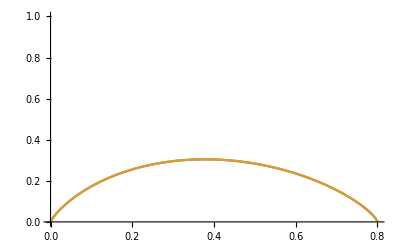

```mathematica
Plot[{
m(-Log[m/(1-0.2)])^((γ-1.)/γ),
m(-Log[(m+0.0001)/(1-0.2)])^((γ-1.)/γ)
},
{m,0,1},
PlotRange->{0,1}
]
```

```mathematica
Plot3D[
0.7m(-Log[m/p])^((γ-1.)/γ),
{m,0,1},
{p,0,1},
AxesLabel->Automatic

]
```

-Graphics3D-

#### Check

```mathematica
{solutionCheck}=solveCheck
```

NDSolve`ProcessEquations::deqn: Equation or list of equations expected instead of solPDE in the first argument solPDE.

Set::shape: Lists {solutionCheck} and $Failed are not the same shape.

$Failed

```mathematica
solutionCheck["FiniteElementData"]["Properties"][[2]]["Properties"]
```

Part::partw: Part 2 of solutionCheck[FiniteElementData][Properties] does not exist.

solutionCheck[FiniteElementData][Properties]⟦2⟧[Properties]

```mathematica
c=({{1, 0}, {0, v(x,y)}});
alpha={0,-u[x,y]};
NDSolveValue[{
{
-((c.u[x,y]{x,y}Inactive){x,y}Inactive)==0,
-((alpha×v[x,y]){x,y}Inactive)==0
},
{u[0,y]==1,v[0,y]==1}
},{u[x,y],v[x,y]},
{x,y}∈Disk[]
]
```

DiscretizeBoundaryConditions::bcnop: No places were found on the boundary where x==0. was True, so DirichletCondition[u==1,x==0.] will effectively be ignored.

DiscretizeBoundaryConditions::bcnop: No places were found on the boundary where x==0. was True, so DirichletCondition[v==1,x==0.] will effectively be ignored.

{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}

```mathematica
Plot3D[InterpolatingFunction[…][x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
c={{1,0},{0,v[x,y]}};
alpha={0,-u[x,y]};
NDSolveValue[{-((c.u[x,y]{x,y}Inactive){x,y}Inactive)==0,-((alpha×v[x,y]){x,y}Inactive)==0},{u[x,y],v[x,y]},{x,y}∈Disk[]]
```

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {u,v}; the result may not be unique.

{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}

```mathematica
c={{1,0},{0,v[x,y]}};
alpha={0,-u[x,y]};
NDSolveValue[{{-((c.u[x,y]{x,y}Inactive){x,y}Inactive)==0,-((alpha×v[x,y]){x,y}Inactive)==0}},{u[x,y],v[x,y]},{x,y}∈Disk[]]
```

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {u,v}; the result may not be unique.

{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}

### Решение

```mathematica
pde=eq/.flux/.rate//.rep;
pde=Activate[pde]//N//FullSimplify;
ics=(ics//.rep)//N;
bcs=(bcs//.rep)//N;

ics
TableForm[pde] == TableForm[bcs]
```

{{n[0.,x,y],p[0.,x,y]}=={0.1,0.001}}

0.+(-0.2+0.19 p[t,x,y]) n^(0,0,2)[t,x,y]+(-0.2+0.19 p[t,x,y]) n^(0,2,0)[t,x,y]+n[t,x,y] (-0.19 p^(0,0,2)[t,x,y]-0.19 p^(0,2,0)[t,x,y])+n^(1,0,0)[t,x,y]
-4. If[2.<x<3.&&2.<y<3.&&1. n[t,x,y]+1. p[t,x,y]≤0.9999,0.7 (-1. Log[(1.-1. n[t,x,y]-1. p[t,x,y])/(1.-1. n[t,x,y])])^0.75 (1.-1. n[t,x,y]-1. p[t,x,y]),0.]-0.01 p^(0,0,2)[t,x,y]-0.01 p^(0,2,0)[t,x,y]+1. p^(1,0,0)[t,x,y]==NeumannValue[0.,x==-1.||x==5.||y==-1.||y==5.]
NeumannValue[0.,x==-1.||x==5.||y==-1.||y==5.]

```mathematica
Mon[Hold[sol=solve]]
```

45.9219

### Графики

#### 1D

```mathematica
(*
Шаг сетки для графика
*)
tstep = 0.1;
xstep = 0.01;

(*
Образование простых функций для вывода
*)
SOLn=
Table[
Table[
n[it,ix]/.sol,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLn=ListInterpolation[SOLn,({{0, tmax}, {xmin, xmax}})];
SOLm=
Table[
Table[
1-n[it,ix]-p[it,ix]/.sol,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLm=ListInterpolation[SOLm,({{0, tmax}, {xmin, xmax}})];
SOLp=
Table[
Table[
p[it,ix]/.sol,
{ix,xmin,xmax,xstep}
],
{it,0,tmax,tstep}
];
SOLp=ListInterpolation[SOLp,({{0, tmax}, {xmin, xmax}})];
(*
График
*)

Manipulate[
Plot[
{
SOLp[t,x],
SOLn[t,x],
SOLm[t,x]
},
{x,xmin,xmax},
PlotRange->{-0.1,1.1}
],
{t,0,tmax}
]
```

#### 2D

```mathematica
(*Шаг сетки для графика*)
tstep =0.01;
xstep = 0.05;
```

```mathematica
Monitor[
SOLpList=Table[
p[it,ix,iy]/.sol,
{it,0,tmax,tstep},
{ix,xmin,xmax,xstep},
{iy,xmin,xmax,xstep}];,
{"Solution N: ",it,"/",tmax," ",ProgressIndicator[it,{0,tmax}]}//Row
]
Monitor[
SOLnList=Table[
n[it,ix,iy]/.sol,
{it,0,tmax,tstep},
{ix,xmin,xmax,xstep},
{iy,xmin,xmax,xstep}];,
{"Solution P: ",it,"/",tmax," ",ProgressIndicator[it,{0,tmax}]}//Row
]
```

```mathematica
sn=ListInterpolation[SOLn,({{0, tmax}, {xmin, xmax}, {xmin, xmax}}),InterpolationOrder->3];
sp=ListInterpolation[SOLp,({{0, tmax}, {xmin, xmax}, {xmin, xmax}}),InterpolationOrder->3];
```

График

```mathematica
cord=y==2;
```

```mathematica
Manipulate[Show[Plot3D[
{
sp[it,x,y],
sn[it,x,y],
1-sn[it,x,y]-sp[it,x,y]
},
{x,xmin,xmax},
{y,xmin,xmax},
PlotRange->{-0.1,1.1},
AxesLabel->Automatic],
ContourPlot3D[Evaluate@cord,{x,xmin,xmax},{y,xmin,xmax},{it,0,tmax},PlotRange->{-0.1,1.1}]
],{it,0,tmax,tstep}]
```

```mathematica
.
```

```mathematica
Manipulate[
Plot[
sp[it,x,SolveValues[cord,y][[1]]],
{x,xmin,xmax},PlotRange->{-0.1,1.1}],
{it,0,tmax,tstep}]
```